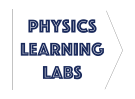
# -Graphics- Lab 3 - Atwood’s Machine

In this lab we will accelerate a Pasco cart via a string tension due to hanging masses. As the hanging masses are varied, the resultant acceleration will be measured and plotted. By determining the line of best fit, we will be able to estimate values of the gravitational acceleration g and kinetic friction μ_k.

## Background

As indicated in the Fig.(1), a smart cart will be accelerated along a ramp via a tension force supplied by a hanging mass. The acceleration will be measured as we vary the cart mass m_c and hanging mass m_h.

In Prelab 3, we derived the equation that governs the acceleration:

a=(m_h-m_c μ_k)/(m_c+m_h)g

## Experiment

### Acceleration Procedure

Open Lab_3.cap and turn on/pair your smart cart.

You must keep the total mass m_h+m_c constant. Start initially with all free masses positioned in the cart (100 g), then for each successive trial, move appropriate free mass onto mass hanger according to Fig.(2) .

Release the cart 25-30 cm away from the position of the rubber bands. Do not exceed this distance when accelerating the cart.

To prevent free masses from moving during the collision, position free masses towards the front of the cart, compacting them as close as possible to each other.

Try a few test runs to familiarize yourself with the procedure.

By taking the slope of velocity plot, record the acceleration according the eight mass combinations given in the figure above. This is the same procedure we used to record the acceleration of the cart in Lab 1.

### Mass Measurement

Using the weigh scale, record the mass of the cart and the empty mass hanger .  Store these values (in kg) as variables mc and mhanger below. Assume the mass of the free individual weights are exact as printed.

```mathematica
mc=
```

```mathematica
mhanger=
```

Store the total mass,  M = m_h+m_c, as variable M below . (Recall that the total mass is constant for every trial. The free masses add up to 100g in total).

```mathematica
M=mc+mhanger+.100;
```

### Data Collection

Record your measurements of the hanging mass and accelerations as the list mydata in the form:

{{m_h_1, a_1}, {m_h_2, a_2}, ...., {m_h_8, a_8}

Here, m_h_i is the total hanging mass (mass hanger + free masses) in kilograms and the a_i are accelerations (m/s^2) derived from dv/dt in Capstone.

```mathematica
mydata =
```

Use ListPlot to plot your data below. Include appropriate axis labels.

```mathematica
ListPlot[mydata,PlotStyle->Red,AxesLabel->{"m_h (kg)","a (m/s^2)"}]
```

### Linear Fitting

To compare our experimental data with the theoretical acceleration equation, we would like our plot to represent a linear function of its independent variable. To accomplish this, first we need to re-express our acceleration equation. Taking x=m_h/M, we may express the acceleration equation in the form

a = -μ_kg+(1+μ_k)gx

This equation takes the linear form a(x)=mx+b. The slope m and intercept b may be determined in terms of physical quantities μ_k and g. You will determine these relationships in the analysis section.

Let’s reformat our data into the linear form (i.e. now as a function of  x=m_h/M )and plot the result.

Using Table, make a list of linear data of the form {{x_i, a_i}, {x_2, a_2}, ...., {x_8, a_8}}  where x_i=m_h_i/M. Store as variable lineardata.

```mathematica
lineardata = Table[{mydata[[i]][[1]]/M,mydata[[i]][[2]]},{i,1,Length[mydata]}];
```

Use ListPlot to store a plot of the linearized data as variable linearplot. Include appropriate axes labels and add option PlotStyle->Red.

```mathematica
linearplot=ListPlot[lineardata,PlotStyle->Red,AxesLabel->{"m_h/M","a (m/s^2)"}]
```

Use the manipulators to vary both both the slope m and the y-intercept b to find the line of best fit of your experimental data (lineardata). The line of best fit is the line that minimizes the sum of the distance between each point and the fit line.

```mathematica
accel[x_,m_,b_]:=m x+b;
xmax = Max[lineardata[[All,1]]];
mmax=13;
bmin = -0.6;
Manipulate[
Show[linearplot,Plot[accel[x,m,b],{x,0,1.1xmax}],AxesLabel->{"m_h/M","a (m/s^2)"}],{{b,-.1,"y-intercept: b"},bmin,0,.001,Appearance->"Open"},{{m,10,"slope: m"},7,mmax,.005,Appearance->"Open"},SaveDefinitions->True]
```

*[If you want more range or precision when adjusting m or b, you may ask TA to modify the above code (or try yourself!)].

## Analysis

### Understanding the Linear Fit

a = -μ_kg+(1+μ_k)gx

Recall that by substituting x=m_h/M we went from a = (m_h-m_c μ_k)/(m_c+m_h)g  to a = -μ_kg+(1+μ_k)gx. 
Eq.(2) now represents the equation of a line a(x) = mx + b.

What are the units of x=m_h/M ?

What is the slope m of Eq.(2), in terms of g and μ_k?

What is the y-intercept b of Eq.(2), in terms of g and μ_k?

Determine μ_k in terms m and b.

Determine g in terms m and b.

What is the advantage of plotting a(x) with x=m_h/M? What does it allow us to determine and how?

### Interpreting Results

Display the graph of the experimental results along with the line of approximate best fit below (right click > copy graphic).

Based on the best fit parameters and your answer to Q5, state the experimental value of g.

Quantitatively compare this to the expected (theoretical) value

Based on the best fit parameters and your answer to Q4, state the experimental value of μ_k.

Using the value of μ_k found above, find the ratio of the gravitational force to the force of friction: (mg/(μ_k N)). Roughly how many times larger is the gravitational force compared to the force of friction?  (Hint: once you determine N, the ratio is simple!).

Based on the acceleration equation a=(m_h-m_c μ_k)/(m_c+m_h)g  , what happens to the acceleration in the limit m_h>> m_c ?

Our equation we derived for the acceleration only applies to a limited system. For example, it assumes a system where the force of friction on the pulley is negligible. List two other assumptions our acceleration model makes.

Summarize this lab. What were the objectives? What did you find? How does this compare to theory? Can you account for any presumable discrepancies in the data?

# Submit this completed notebook as a .pdf into HuskyCT. (Make sure all cells sections are visible to receive credit for all your output. As a shortcut, use CTRL+A then CTRL+SHIFT+[ to open all cell sections).